-Graphics-

# Building Applications with Neural Networks

## Jérôme Louradour Wolfram Research jeromel@wolfram.com

-Graphics-

-Graphics-

## Methodology

### 1) Define the problem to solve

#### Collect Data

Machine Learning is data-driven, so
the quality of the model will strongly depend on the quality of the data

Black art...

Crowdsourcing

-Graphics--Graphics-

Importance of recording conditions: must be varied

"Once upon a time, the US Army wanted to use neural networks to automatically detect camouflaged enemy tanks. [...]. Wisely, the researchers had originally taken 200 photos, 100 photos of tanks and 100 photos of trees. They had used only 50 of each for the training set. The researchers ran the neural network on the remaining 100 photos, and without further training the neural network classified all remaining photos correctly. Success confirmed! The researchers handed the finished work to the Pentagon, which soon handed it back, complaining that in their own tests the neural network did no better than chance at discriminating photos.
It turned out that in the researchers' dataset, photos of camouflaged tanks had been taken on cloudy days, while photos of plain forest had been taken on sunny days. The neural network had learned to distinguish cloudy days from sunny days, instead of distinguishing camouflaged tanks from empty forest. " source: http://intelligence.org/files/AIPosNegFactor.pdf

#### Set Up Evaluation

The performance to assess include:

Quality measurement(s) on some dataset(s)

Processing times

Other specific needs?

Training speed — ex: need to retrain every night

Interpretability

Choosing how to assess robustness may not be obvious.

Detection,Verification,Binary classification | Accuracy / Error Rate,Recall& Precision& F1,ROC curve& AUC,DET curve
Classification | Accuracy / Error Rate, Micro- or Macro-Recall & Precision & F1
Ranking (Recommendation,Information Retrieval) |  Precision@n, MAP, Normalized DCG, Mean Reciprocal Rank, Kendal’s Tau, Spearman’s Rho, ...
Translation |  BLEU score (% of 4-gram of the evaluated translation that is in the human translation)
Transduction: Audio and Text Recognition | Phoneme/Character Error Rate and Word Error Rate (WER) computed byEdit Distance
Language Model | Perplexity

Nothing is more neat and clear than Benchmark tables:

```mathematica
Row@{With[{results=<|"Dataset 1"-><|"Error%":>RandomReal[{1.7,2}],"100-F1%":>100-RandomReal[{95,97}]|>,"Dataset 2"-><|"Error%":>RandomReal[{10,13}],"100-F1%":>100-RandomReal[{85,86}]|>,"Dataset 3"-><|"Error%":>RandomReal[{45,50}],"100-F1%":>100-RandomReal[{60,70}]|>,"…"-><||>|>},
Labeled[Dataset[<|"System 1"->results,"System 2"->0.92*results,"…"->results/.x_/;NumericQ[x]:>""|>],Text@"Performance Assessment on Test Data"]],
"\t",
With[{results=<|"Size 1" -> <|"CPU":>RandomReal[{0.5,0.7}],"GPU":>RandomReal[{0.08,0.1}]|>,"Size 2"-><|"CPU":>RandomReal[{3,4}],"GPU":>RandomReal[{0.5,0.7}]|>,"…"-><||>|>},
Labeled[Dataset[<|"System 1"->results,"System 2"->3*results,"…"->results/.x_/;NumericQ[x]:>""|>],Text@"Processing Time"]]}
```

Dataset[<>]Performance Assessment on Test Data	Dataset[<>]Processing Time

Differences in performance are sometimes not significative. Ideally one should do:

Statistical Paired Difference Test (like Student’s t-test)

Visualize the variance of the results with Box Whister Chart on subsets of the testset

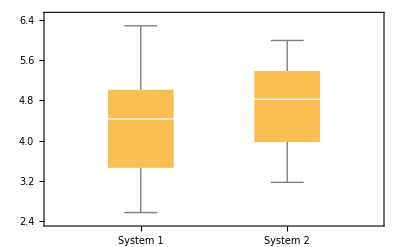

```mathematica
BoxWhiskerChart[{RandomReal[NormalDistribution[4.5,1],60],RandomReal[{3,6},60]},ChartLabels->{"System 1", "System 2"}]
```

### 2) Make the best system you can

#### Data Splits and Strategies

-Graphics-

#### Adapt a Pretrained Model!

Use Transfer Learning and avoid building a Net from scratch!

The Wolfram Neural Net Repository is a good start

The architecture details that you probably care about for the Net “Surgery”:

Output Layers

Loss Function

Regularization: DropoutLayer, BatchNormalizationLayer, NormalizationLayer, ...

#### Some tricks

Data Augmentation: Generate random realistic noise that could not be well filtered out by some pre-processing (the complementary approach)

Hyper-parameter tuning:

Front-End Processing & Data Augmentation

Net Architecture (connectivity patterns, non-linearities, number of hidden units ...)

Optimization (initialization, learning rate schedule, regularization, loss function ...)

How to know if collecting data would help in the current setting? → Learning Curves

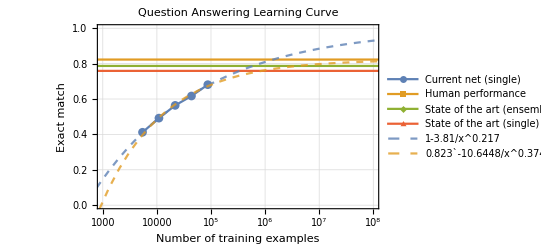

Skip connections seem to be part of the success

-Graphics- | -Graphics- | -Graphics- | -Graphics-
ResNet | Highway network | DenseNet | U-Net

### 3) Monitor and Re-Iterate

Once you have a first good system, you can maybe improve the training data and loop (bootstrapping)

-Graphics--Graphics-
Baron Munchausen pulls himself out of a mire by his own hair.

## Classify Audio Samples

Find data on the web:

```mathematica
scrapeAudio[string_]:=Thread[WebAudioSearch[string,"Samples",Function[#Duration>4&&#Duration<8],MaxItems->30]->string]
```

Be smart to get data

```mathematica
classes={"cow","bird","cat"};
```

```mathematica
animalSounds=Union@@Map[scrapeAudio,classes];
```

Watch your data

```mathematica
RandomSample[animalSounds,3]
```

{→bird,→bird,→cow}

Explicit train/validation[/test] split is always better than implicit

```mathematica
{train,valid}=TakeList[RandomSample[animalSounds],{60,All}];
```

Let’s choose a (first) Net to try:

```mathematica
NetModel["VGGish Feature Extractor Trained on YouTube Data"]
```

NetMapOperator[<>]

```mathematica
NetReplacePart[NetModel["VGGish Feature Extractor Trained on YouTube Data"],"Output"->None]
```

NetMapOperator[<>]

Use this Net as a feature extractor into a bigger Net that classifies sequence (using max-pooling):

```mathematica
classifier=NetGraph[<|
"features"->NetModel["VGGish Feature Extractor Trained on YouTube Data"],
"dropout" -> DropoutLayer[],
"linear"->NetMapOperator[LinearLayer[]],
"max"->AggregationLayer[Max,1],
"softmax"->SoftmaxLayer["Output"->NetDecoder[{"Class",classes}]]
|>, {"features"->"dropout"->"linear"->"max"->"softmax"}]
```

NetGraph[<>]

Train with early-stopping and monitor a set of acknowledged classification performance measurements:

```mathematica
trainres=NetTrain[classifier,train,All,ValidationSet->valid,
TrainingProgressMeasurements->{"ConfusionMatrix","ErrorRate","Precision","Recall","F1Score"},
TrainingStoppingCriterion-><|"Criterion"->"ErrorRate","Patience"->5|>,
TargetDevice->"GPU"]
```

NetTrain Results
summary | ,,  batches:40  rounds:20  time:12s  examples/s:112
data | ,,  training examples:60  validation examples:30  processed examples:1280  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:2.5×10^-3  error:0%  prec.:100%  recall:100%  F1:100%
validation | ,,  loss:2.13  error:30.0%  prec.:67.6%  recall:67.6%  F1:67.4%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainres["ValidationMeasurements"]
```

<|Loss→2.13487,ConfusionMatrix→SparseArray[…],ErrorRate→0.3,Precision→<|cow→0.846154,bird→0.625,cat→0.555556|>,Recall→<|cow→0.846154,bird→0.555556,cat→0.625|>,F1Score→<|cow→0.846154,bird→0.588235,cat→0.588235|>|>

## Optical Character Recognition (OCR)

### Table of Content

We will see how to implement 3 approaches:

With RNN and CTC decoder

-Graphics-

With a CNN that classifies pixels (as in image segmentation)

-Graphics-

With Seq-2-Seq (RNN with Attention)

-Graphics-

### RNN and CTC decoding

Make a dataset that maps images of words to the corresponding words (as strings):

Start simple for a first Proof Of Concept (POC)

```mathematica
fonts = Take[$FontFamilies, 10]

imageWord[word_String] := Rasterize[
		Style[word,
			FontFamily -> RandomChoice[fonts],
			FontSize -> RandomInteger[{18, 22}]
		], Background -> Lighter[RandomColor[], 0.8]
	];
	
labeledImageWord[word_String] := imageWord[word] -> word
```

{aakar,Abyssinica SIL,Alegreya SC,Andale Mono,Ani,AnjaliOldLipi,Arial,Arial Black,Bitstream Charter,Bitstream Vera Sans}

```mathematica
imageWord["word"]
```

-Graphics-

```mathematica
labeledImageWord["LabeledWord"]
```

-Graphics-→LabeledWord

For the sake of reproducibility and to avoid losing time:

Use seeds for random thing

Store intermediate steps of data construction

When processing the full dataset is long (>>1H), store the progress to be able to restart at the point in case of failure

```mathematica
SeedRandom[123]
data = ParallelMap[labeledImageWord, ToLowerCase[RandomSample[WordList["CommonWords"], 10000]]]; // AbsoluteTiming
```

{11.1326,Null}

```mathematica
RandomSample[data,10]//Column
```

-Graphics-→hushed
-Graphics-→irrigate
-Graphics-→spectrometric
-Graphics-→consoling
-Graphics-→unguent
-Graphics-→plantain
-Graphics-→clack
-Graphics-→townsman
-Graphics-→camaraderie
-Graphics-→discombobulated

Don’t forget Data Augmentation to be robust to noise!

```mathematica
noiseImage[image_] := ImageEffect[Blur[image, RandomReal[1.5]], {"GaussianNoise", RandomReal[0.1]}]
noiseImage[image_ -> label_] := noiseImage[image] -> label
```

```mathematica
noisedData = ParallelMap[noiseImage, data];//AbsoluteTiming
```

{3.61776,Null}

```mathematica
RandomSample[noisedData,10]//Column
```

-Graphics-→perversion
-Graphics-→sanctification
-Graphics-→hamburger
-Graphics-→analyzer
-Graphics-→perish
-Graphics-→reshipment
-Graphics-→expanse
-Graphics-→crackling
-Graphics-→absentmindedness
-Graphics-→outlawry

```mathematica
{trainset,validset,testset}=TakeList[noisedData,{8000,1000,All}];
```

```mathematica
Length/@{trainset,validset,testset}
```

{8000,1000,1000}

Make a preprocessing that convert the image and resize it to a fixed height (of 18):

```mathematica
preprocFunction = ImageData @*
	Function[ImageReflect[#, Left->Top]] @*
	Function[ImageResize[#, {Automatic, 18}]] @*
	Function[ColorConvert[#, "Grayscale"]];
```

Each row is a feature that corresponds to a vertical line of pixels in the input image:

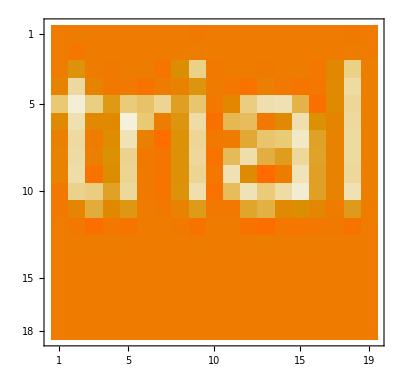

```mathematica
preprocFunction[imageWord["trial"]]//Transpose//MatrixPlot
```

Make a NetEncoder containing this pre-processing function, that we will attach to the network:

```mathematica
preproc = NetEncoder[{"Function", preprocFunction, {"Varying", 18}, "Pattern" -> _Image}]
```

NetEncoder[<>]

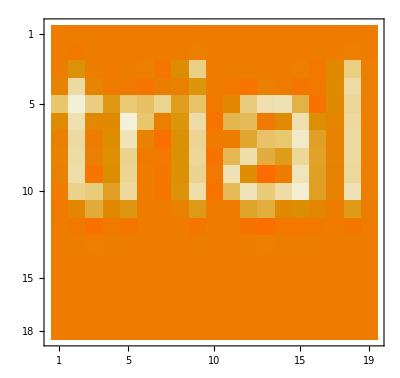

```mathematica
preproc[imageWord["trial"]]//Transpose//MatrixPlot
```

Now let’s worry about the output of the Net, which will be managed with CTC

```mathematica
chars = Flatten[Characters@Values[trainset]];
vocabulary = Union[chars]
```

{-,',a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Look at some analysis of the data, to detect some potential problems (in the data or your process)

```mathematica
Dataset @ ReverseSort @ Counts[chars]
```

Dataset[<>]

The post-processing of the net is a NetDecoder["CTCBeamSearch"]:

```mathematica
postproc = NetDecoder[{"CTCBeamSearch", vocabulary, "BeamSize" -> 50}]
```

NetDecoder[<>]

The corresponding Loss function is:

```mathematica
loss = CTCLossLayer["Target" -> NetEncoder[{"Characters", vocabulary}]]
```

CTCLossLayer[<>]

Note the presence of NetEncoder["Characters"] that means “process the strings in the “Target” port as a list of characters”

Make a Network with Convolutions and Bidirectional LSTMs:

```mathematica
ctcNet = NetChain[
	{
		ConvolutionLayer[64, {3}, "PaddingSize"->1, "Interleaving"->True], Tanh,
		NetBidirectionalOperator[LongShortTermMemoryLayer[64, "Dropout" -> <|"VariationalInput" -> 0.5|>], Catenate],
		ConvolutionLayer[128, {3}, "PaddingSize"->1, "Interleaving"->True], Tanh,
		NetBidirectionalOperator[LongShortTermMemoryLayer[128, "Dropout" -> <|"VariationalInput" -> 0.5|>], Total],
		DropoutLayer[],
		NetMapOperator[LinearLayer[]],
		SoftmaxLayer[]
	},
	"Input" -> preproc,
	"Output" -> postproc	
]
```

NetChain[<>]

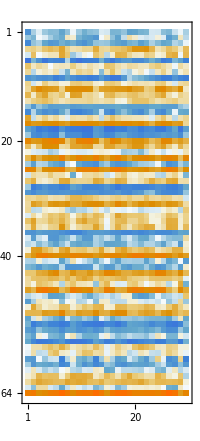
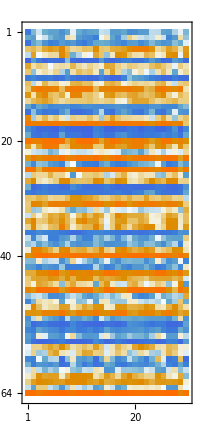
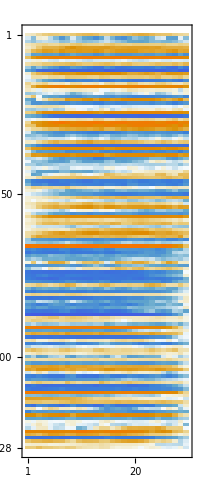
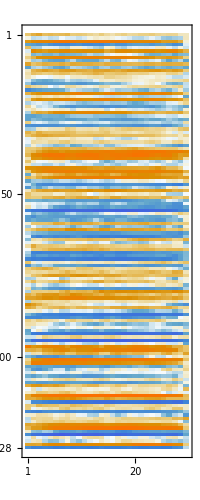
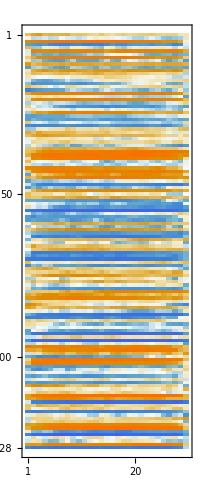
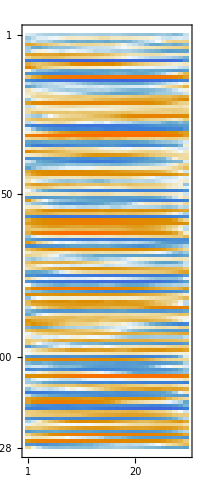
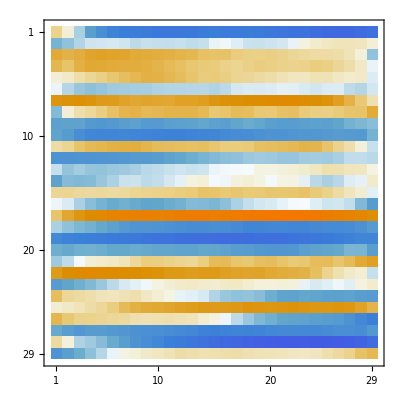
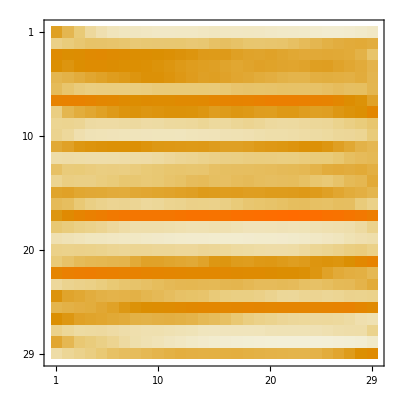
<|NetPort[{1,Output}]→-Graphics-,NetPort[{2,Output}]→-Graphics-,NetPort[{3,Output}]→-Graphics-,NetPort[{4,Output}]→-Graphics-,NetPort[{5,Output}]→-Graphics-,NetPort[{6,Output}]→-Graphics-,NetPort[{7,Output}]→-Graphics-,NetPort[{8,Output}]→-Graphics-,NetPort[{9,Output}]→-Graphics-|>

```mathematica
MatrixPlot/@Transpose/@NetInitialize[ctcNet][imageWord["trial"],NetPort[All]]
```

Train the Net:

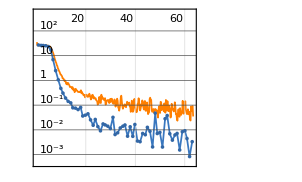
NetTrain Results
summary | ,,  batches:15804  rounds:64  time:19min  examples/s:450
data | ,,  training examples:8000  validation examples:1000  processed examples:505728  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:6.08×10^-2
validation | ,,  loss:3.33×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

NetChain[<>]

```mathematica
filename = FileNameJoin[{NotebookDirectory[], "NetTrainResultsObject_OCR_CTC.wdx"}];
result = If[FileExistsQ[filename], Import[filename],
	result = NetTrain[
		ctcNet, trainset, All,
		LossFunction -> loss, ValidationSet -> validset,
		TrainingStoppingCriterion -> <|"Criterion" -> "Loss", "Patience" -> 7|>, MaxTrainingRounds -> Quantity[3600, "Seconds"],
		TargetDevice -> "GPU"
	];
	Export[filename, result];
	result
]
trainedNet = result["TrainedNet"]
```

Dump training results in files (also during training!)

Let’s see how does the network:

Evaluate the character error rate on the test set:

```mathematica
N@Mean@MapThread[EditDistance[#1,#2]&,
{trainedNet[First/@testset,TargetDevice->"GPU"],
Characters[Last/@testset]}]
```

0.001

```mathematica
trainedNet[-Graphics-]
```

{k,a,d,i,d,d,l,e,h,o,p,p,e,r}

```mathematica
trainedNet[-Graphics-]
```

{l,o,n,g,s,e,q,u,e,n,c,e,o,f,c,h,a,r,a,c,t,e,r,s}

```mathematica
trainedNet[-Graphics-]
```

{v,e,r,y,l,o,n,g,r,e,p,e,a,t,e,d,s,e,q,u,e,n,c,e,o,f,c,h,a,r,a,c,t,e,r,s,v,e,r,y,l,o,n,g,r,e,p,e,a,t,e,d,s,e,q,u,e,n,c,e,o,f,c,h,a,r,a,c,t,e,r,s,v,e,r,y,l,o,n,g,r,e,p,e,a,t,e,d,s,e,q,u,e,n,c,e,o,f,c,h,a,r,a,c,t,e,r,s,v,e,r,y,l,o,n,g,r,e,p,e,a,t,e,d,s,e,q,u,e,n,c,e,o,f,c,h,a,r,a,c,t,e,r,s}

```mathematica
trainedNet[-Graphics-]
```

{r,c,w,i,y,t}

```mathematica
trainedNet[-Graphics-]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,o,i,z,d,d,b,z,f,l,i,-,-}

All the properties of NetDecoder["CTCBeamSearch"] can be used:

```mathematica
NetExtract[trainedNet,"Output"]
```

NetDecoder[<>]

```mathematica
trainedNet[-Graphics-,{"TopNegativeLogLikelihoods",1}]
```

{{s,c,h,m,i,l,b,l,i,c,k}→1.85005×10^-6}

Let’s do a trick to see how CTC decoding works.
Replace the NetDecoder[“CTCBeamSearch”] for a NetDecoder[“Class”] to do framewise classification including the “blank” label

```mathematica
trainedNetClassDecoder=NetReplacePart[trainedNet,
"Output"->NetDecoder[{"Class",Append[NetExtract[trainedNet,{"Output","Labels"}], "_"]}]]
```

NetChain[<>]

```mathematica
trainedNetClassDecoder[-Graphics-]
```

{_,s,s,_,_,_,_,_,_,_,c,_,_,h,_,_,_,_,_,_,_,_,_,m,m,_,_,_,_,_,_,_,i,i,_,_,_,l,_,_,_,b,_,_,_,_,_,_,_,l,_,_,i,i,_,_,_,_,_,_,c,c,_,_,_,_,_,_,_,k,k}

Let’s try to see inside the black box.

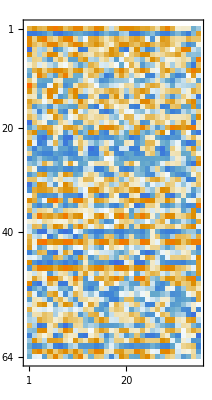
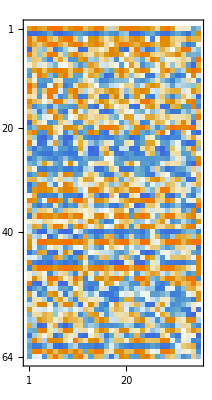
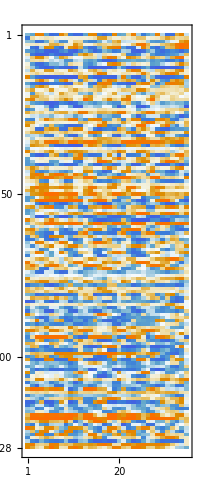
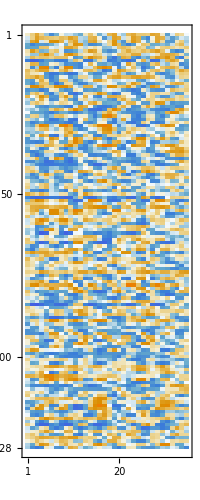
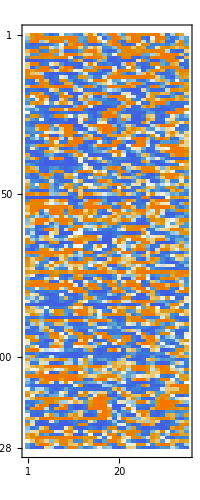
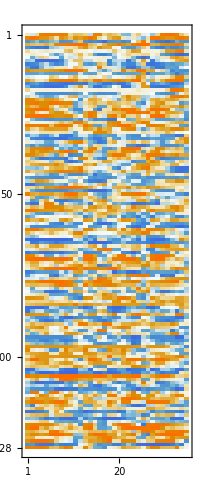
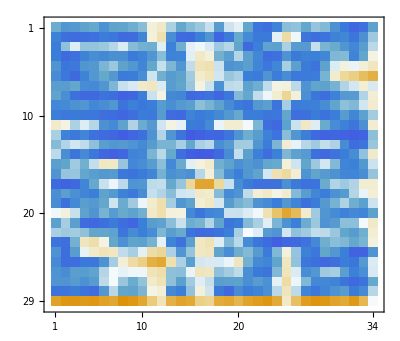
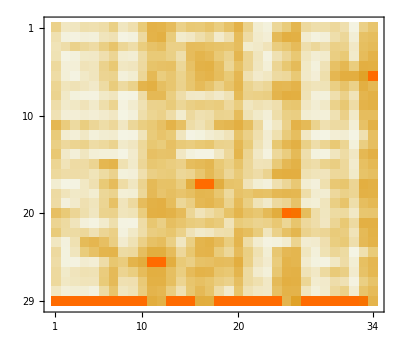
<|NetPort[{1,Output}]→-Graphics-,NetPort[{2,Output}]→-Graphics-,NetPort[{3,Output}]→-Graphics-,NetPort[{4,Output}]→-Graphics-,NetPort[{5,Output}]→-Graphics-,NetPort[{6,Output}]→-Graphics-,NetPort[{7,Output}]→-Graphics-,NetPort[{8,Output}]→-Graphics-,NetPort[{9,Output}]→-Graphics-|>

```mathematica
MatrixPlot/@Transpose/@trainedNet[-Graphics-,NetPort[All]]
```

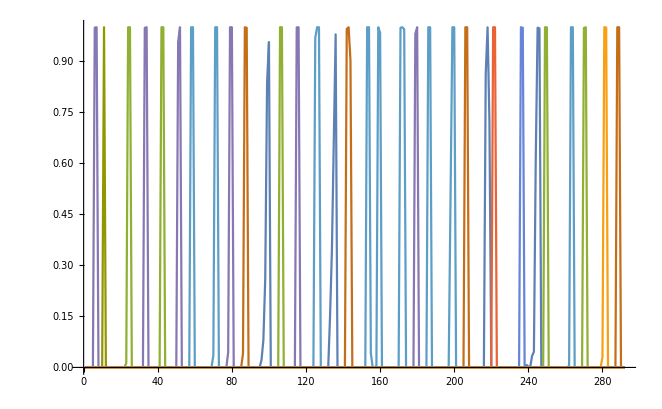

```mathematica
ListLinePlot[Most@Transpose@trainedNet[-Graphics-,None],PlotRange->All]
```

Let’s try to interpolate the localization of the characters based on the raw output of the net:

```mathematica
spotCharacters[net_, image_] := Module[{charprobas, vocsize, argmax, colors, imgwidth, imgheight},
	charprobas = net[image, None];
	vocsize = Last @ Dimensions[charprobas];
	argmax = Map[First @ Ordering[#, -1]&, charprobas];
	colors = Map[If[#===vocsize, Transparent, ColorData["Rainbow"][#/vocsize]]&, argmax];
	{imgwidth, imgheight} = ImageDimensions[image];
	Column[{
		Fold[
			Function @ ImageCompose[#1,
				With[{
					width = Round[imgwidth*Last[#2]/Length[charprobas]]-Round[imgwidth*(Last[#2]-1)/Length[charprobas]],
					height = Floor[imgheight/2]},
					ConstantImage[First[#2],{width, height}]
				],
				{Round[imgwidth*Last[#2]/Length[charprobas]]-1,1}
			],
			image, MapIndexed[{#1,First[#2]}&, colors]
		],
		Row@Map[Style[#, Large, ColorData["Rainbow"][First@FirstPosition[vocabulary,#]/vocsize]]&, net[image]]
	}]
]
```

We note that LSTM along with CTC does hardly provide a localization of the recognized characters (not designed for that).

```mathematica
spotCharacters[trainedNet,-Graphics-]
```

-Graphics-
characters-are-detected-by-peaks

Next steps:

...

### CNN Pixel Classifier (Image Segmentation)

Let’s make the data with labeled character location.

The components of the binarized image can be used for that:

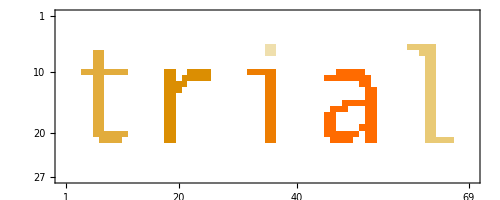

```mathematica
MorphologicalComponents[ColorNegate@MorphologicalBinarize@imageWord["trial"]]//MatrixPlot
```

Pixel localization will be done by the Net after a resize and transpose of the image:

the target depends on the pre-processing

the post-processing should retrieve localization in the original image

The part of the preprocessing that will change image coordinates will be:

```mathematica
imageTransform =
	Function[ImageReflect[#, Left->Top]] @*
	Function[ImageResize[#, {Automatic, 18}]]
```

ImageReflect[#1,Left→Top]&@*(ImageResize[#1,{Automatic,18}]&)

```mathematica
getLocalizationLabels[image_, word_] := Module[{components, charlabels, ilabel, componentsMap, new, known},
	components = MorphologicalComponents[ColorNegate @ MorphologicalBinarize[imageTransform[image]]];
	charlabels = Characters[word];
	ilabel = 0;
	componentsMap = <|0 -> ""|>;
	Map[
		Function[
			If[MemberQ[#, Except[Alternatives @@ Keys[componentsMap]]],
				(* Hit a new letter *)
				new = Complement[#, Keys[componentsMap]];
				If[Length[DeleteCases[Intersection[#, Keys[componentsMap]], 0]] == 0,
					++ilabel;
				];
				componentsMap = Append[componentsMap, AssociationMap[charlabels[[ilabel]]&, new]];
				
			];
			# /. componentsMap
		],
		components
	]
]
```

```mathematica
getLocalizationLabels[-Graphics-,"trial"]//Style[Grid[Transpose[#],Frame->True],Tiny]&
```

|  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  |  |  |  |  |  |  |  |  |  | l | l | l |  |  |  | 
 |  |  | t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | l |  |  |  | 
 |  |  | t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | l |  |  |  | 
 |  | t | t | t | t | t |  |  |  |  | r | r |  | r | r |  |  |  |  | i | i | i | i |  |  |  |  |  |  | a | a | a |  |  |  |  |  |  |  | l |  |  |  | 
 |  |  | t | t |  |  |  |  |  |  | r | r | r |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  | a |  |  |  | a |  |  |  |  |  |  | l |  |  |  | 
 |  |  | t |  |  |  |  |  |  |  | r | r |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  |  |  |  |  | a | a |  |  |  |  |  | l |  |  |  | 
 |  |  | t |  |  |  |  |  |  |  | r | r |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  |  |  | a | a | a | a |  |  |  |  |  | l |  |  |  | 
 |  |  | t |  |  |  |  |  |  |  | r | r |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  | a | a | a |  | a | a |  |  |  |  |  | l |  |  |  | 
 |  |  | t |  |  |  |  |  |  |  | r | r |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  | a |  |  |  | a | a |  |  |  |  |  | l |  |  |  | 
 |  |  | t | t |  |  |  |  |  |  | r | r |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  | a |  |  | a | a |  |  |  |  |  |  | l |  |  |  | 
 |  |  |  | t | t | t |  |  |  |  | r | r |  |  |  |  |  |  |  |  |  | i | i |  |  |  |  |  | a | a | a | a | a | a |  |  |  |  |  | l | l | l |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
toLabeledLocalization[image_ -> word_] := Quiet @ Check[
	image -> getLocalizationLabels[image, word],
	Nothing
]
```

```mathematica
localdata=ParallelMap[toLabeledLocalization,data];
```

Anticipate failures in the pre-processing, and it is OK to ignore problems on some data if it concerns a small portion of your data.

```mathematica
localdata//Length
```

6811

```mathematica
RandomSample[localdata,3]//MapAt[Style[Grid[Transpose[#],Frame->True],Tiny]&,{All,2}]
```

{-Graphics-→ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | t |  |  |  |  |  |  |  |  |  |  |  | t |  |  |  |  |  |  |  |  |  |  |  |  | t |  |  |  | i |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | t |  |  |  |  |  |  |  |  |  |  |  | t |  |  |  |  |  |  |  |  |  |  |  |  | t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | o | o |  |  |  |  |  |  |  |  |  |  |  |  |  | t | t |  |  |  |  | s | s |  |  |  | t | t | t |  |  |  |  | a | a |  |  |  |  | t | t | t |  |  |  |  |  |  |  | o | o |  |  |  |  |  |  |  | n | n |  |  | 
 |  | o | o | o | o | o |  |  | u | u |  |  |  | u | u |  |  | t | t |  |  | s | s | s | s | s |  |  | t | t | t |  |  | a | a | a | a | a | a |  |  | t | t | t |  |  | i |  |  |  | o | o | o | o | o |  |  | n | n | n | n | n | n |  | 
 | o |  |  |  |  | o | o |  | u | u |  |  |  | u | u |  |  | t | t |  |  | s |  |  |  | s | s |  |  | t |  |  |  | a |  |  |  |  | a |  |  |  | t |  |  |  | i |  |  | o |  |  |  |  | o | o |  |  | n |  |  |  | n | n | 
 | o |  |  |  |  | o | o |  | u | u |  |  |  | u | u |  |  | t | t |  |  | s | s | s |  |  |  |  |  | t |  |  |  |  |  |  |  | a | a |  |  |  | t |  |  |  | i |  |  | o |  |  |  |  | o | o |  | n | n |  |  |  |  | n | 
 | o |  |  |  |  | o | o |  | u | u |  |  |  | u | u |  |  | t | t |  |  |  | s | s | s | s |  |  |  | t |  |  |  |  | a | a | a | a | a |  |  |  | t |  |  |  | i |  | o | o |  |  |  |  | o | o |  | n | n |  |  |  |  | n | 
 | o |  |  |  |  | o | o |  | u | u |  |  |  | u | u |  |  | t | t |  |  |  |  |  |  | s | s |  |  | t |  |  |  | a |  |  |  |  | a |  |  |  | t |  |  |  | i |  |  | o |  |  |  |  | o | o |  | n | n |  |  |  |  | n | 
 | o | o |  |  |  | o |  |  | u | u |  |  |  | u | u |  |  | t | t |  |  | s |  |  |  |  | s |  |  | t |  |  |  | a |  |  |  | a | a |  |  |  | t |  |  |  | i |  |  | o | o |  |  |  | o |  |  | n | n |  |  |  |  | n | 
 |  | o | o | o | o | o |  |  |  | u | u | u | u | u | u |  |  | t | t | t |  | s | s | s | s | s |  |  |  | t | t | t |  | a | a | a | a | a | a | a |  |  | t | t |  |  | i |  |  |  | o | o | o | o | o |  |  | n | n |  |  |  |  | n | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | ,-Graphics-→ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | e | e |  | l | l |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | e | e |  |  | l |  |  |  |  |  |  |  |  |  |  |  | e |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | e |  |  |  | l |  |  |  |  |  |  |  |  |  |  |  | e | e | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | e |  |  |  | l |  |  |  |  |  |  |  |  |  |  |  | e |  | 
 |  |  |  |  | r |  |  |  |  |  |  |  |  |  | p |  |  |  |  | e |  |  |  | l |  |  |  | l |  |  |  |  | e | e | e | e |  | 
r | r | r |  | r | r | r |  |  |  | e | e |  |  | p | p | p | p |  |  | e |  |  |  | l |  |  | l | l | l |  |  | e | e |  | e |  |  | 
r |  | r | r | r | r |  |  |  |  |  |  | e |  | p | p |  |  |  |  | e |  |  |  | l |  | l | l | l |  |  |  |  |  |  | e |  |  | 
r |  |  |  | r |  | r |  |  |  | e |  | e |  |  | p |  | p |  |  | e | e |  |  | l |  |  | l |  | l |  |  |  |  |  | e | e |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | e |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | ,-Graphics-→ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | s | s | s | s |  |  | u | u |  |  | u |  |  |  | c | c | c | c |  |  | k | k |  |  | k |  |  | l | l |  |  |  |  | i | i |  |  | n | n |  |  | n | n |  |  |  | g | g | g | g | 
 | s |  |  | s |  |  | u |  |  |  | u |  |  | c |  |  |  |  |  |  |  | k |  | k |  |  |  |  | l |  |  |  |  | i |  |  |  |  | n | n |  |  | n |  |  | g |  |  |  | g | 
 | s | s |  |  |  |  | u |  |  |  | u |  |  | c |  |  |  |  |  |  |  | k | k |  |  |  |  |  | l |  |  |  |  | i |  |  |  | n |  | n |  |  | n |  | g | g |  |  |  |  | 
 |  | s | s | s |  |  | u |  |  |  | u |  |  | c |  |  |  |  |  |  |  | k | k |  |  |  |  |  | l |  |  |  |  | i |  |  |  | n |  |  | n |  | n |  | g |  |  |  | g | g | 
 |  |  |  | s |  |  | u |  |  |  | u |  |  | c |  |  |  |  |  |  |  | k |  | k |  |  |  |  | l |  |  |  |  | i |  |  |  | n |  |  | n | n | n |  | g | g |  |  |  | g | 
 | s |  |  | s |  |  | u | u |  | u | u |  |  |  | c |  |  | c |  |  | k | k |  |  | k |  |  | l | l |  | l | l |  | i |  |  |  | n |  |  |  | n | n |  |  | g | g |  | g | g | 
 |  | s |  |  |  |  |  |  | u |  |  |  |  |  |  | c | c |  |  |  | k | k |  |  |  |  |  | l | l | l | l |  |  | i | i |  |  | n |  |  |  |  |  |  |  |  |  | g |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }

```mathematica
noisedLocaldata=ParallelMap[noiseImage,localdata];
```

```mathematica
RandomSample[noisedLocaldata,3]//MapAt[Style[Grid[Transpose[#],Frame->True],Tiny]&,{All,2}]
```

{-Graphics-→ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | b |  |  |  |  |  |  |  |  |  |  |  | b | b |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | i |  |  |  |  |  |  |  |  | i |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | b |  |  |  |  |  |  |  |  |  |  |  | b |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | t |  |  | t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | b | b | b | b |  |  |  | a | a | a |  |  |  | b | b | b |  |  |  |  |  |  |  |  |  | s | s | s |  |  | i |  |  | t | t |  | t | t |  |  |  |  | n |  | n | n |  |  |  | g | g | g | g | 
 | b | b |  | b | b |  | a |  |  |  | a |  |  | b |  |  | b |  |  | y |  |  | y |  | s | s |  |  | s |  | i |  |  | t |  |  | t | t |  | i |  |  | n | n |  | n | n |  | g | g |  |  | g | 
 | b |  |  |  | b |  |  |  |  | a | a |  | b | b |  |  |  | b |  | y |  |  | y |  | s | s |  |  |  |  | i |  |  | t |  |  | t |  |  | i |  |  | n |  |  |  | n |  | g |  |  |  | g | 
 | b |  |  |  | b |  | a | a |  | a | a |  |  |  |  |  |  | b |  | y |  | y | y |  |  |  | s | s | s |  | i |  |  | t |  |  | t |  |  | i |  |  | n |  |  |  | n |  | g |  |  |  | g | 
 | b |  |  |  | b |  | a |  |  |  | a |  |  | b |  |  | b |  |  |  | y | y |  |  | s |  |  |  | s |  | i |  |  | t |  |  | t |  |  | i |  |  | n |  |  |  | n |  | g |  |  |  | g | 
 | b | b | b | b |  |  | a | a | a | a | a |  |  | b | b | b | b |  |  |  | y | y |  |  |  | s | s | s |  |  | i |  |  | t | t |  |  | t |  | i |  |  | n |  |  |  | n |  |  | g | g | g | g | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | y |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | g | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | y | y |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | g | g |  | g | g | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | y |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | g | g |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | ,-Graphics-→ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | b | b |  |  | l | l |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  | b | b |  |  |  | l |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  | i |  |  |  |  |  |  | l |  |  | i |  |  |  |  |  |  |  |  |  | 
 |  |  |  | i | i |  |  |  |  |  |  | l |  |  | i | i |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  | b | b |  |  | l |  |  |  |  |  |  | n | n |  |  |  |  | 
 | s | s |  |  | i |  |  | b |  | b |  | l |  |  | i |  |  | n |  |  | n | n |  |  | 
 |  |  |  |  | i |  |  |  |  | b |  | l |  |  | i |  |  | n |  |  | n | n |  | n | 
 |  | s |  |  | i |  |  | b | b | b |  | l |  |  | i |  |  |  |  |  |  |  | n | n | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | n |  | n | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | n | n | n | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | ,-Graphics-→ |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
t | t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
t | t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | n | n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
t |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | n | n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
t |  |  |  |  |  |  |  |  |  |  |  |  | a | a |  |  | a |  |  |  |  |  |  | s | s |  |  |  | i | i |  |  | i | i |  |  |  |  |  | 
t |  |  | r | r | r |  |  | a |  | a |  | a | a |  | a | a | a | a |  | n |  |  | s | s | s |  |  | i | i |  | i | i |  |  |  | e |  |  | e | 
t |  |  | r | r |  | r |  | a |  | a |  |  |  |  | a |  |  |  |  | n |  |  | s | s |  |  |  |  |  |  | i |  |  |  |  |  | e | e |  | 
t | t |  |  | r |  |  |  | a | a |  | a | a |  |  |  |  |  | a |  | n | n |  | s |  | s |  |  |  |  |  |  |  | i | i |  |  | e |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }

The pre and post-processing

```mathematica
preprocFunction3D = Function[ArrayReshape[#,Append[Dimensions[#], 1]]] @*
	ImageData @*
	imageTransform @*
	Function[ColorConvert[#, "Grayscale"]];
```

Make a NetEncoder containing this pre-processing function, that we will attach to the network:

```mathematica
preproc3D = NetEncoder[{"Function", preprocFunction3D, {"Varying", 18, 1}, "Pattern" -> _Image}]
```

NetEncoder[<>]

```mathematica
preproc3D[-Graphics-]//Dimensions
```

{29,18,1}

The post-processing will be an elementwise lookup of the classes, with  a NetDecoder["Class"]

```mathematica
classdecoder=NetDecoder[{"Class",Append[vocabulary,""],"InputDepth"->3}]
```

NetDecoder[<>]

This takes an array of probability of depth 3 and returns an array of depth 2 with the classes:

```mathematica
classdecoder[SoftmaxLayer[]@RandomReal[1,{5,18,29}]]//Grid
```

j | v | s | d | m | l | t | v | n | e | g | i | t | j | p | k | y | y
d | - | y | i | s | y | h | j | x | z | u | y | l | g | x | k | e | a
a | e | y | r | r | c | g | q | c | b | u | - | u | o | u | s | b | n
p | t | l | e | r | s | s | i | n | c | u | n | c | t | a | t | u | w
r | s | e | d | u | h | r | x | v | u | g | p | r | b | m | f | q | c

Make a Network with Convolutions and Bidirectional LSTMs:

```mathematica
pxlNet = NetChain[
	{
		ConvolutionLayer[64, {5, 5}, "PaddingSize"->2, "Interleaving"->True], Ramp,
		DropoutLayer[],
		ConvolutionLayer[128, {5, 5}, "PaddingSize"->2, "Interleaving"->True], Ramp,
		DropoutLayer[],
		ConvolutionLayer[128, {5, 5}, "PaddingSize"->2, "Interleaving"->True], Ramp,
		DropoutLayer[],
		ConvolutionLayer[Automatic, {1, 1}, "Interleaving"->True],
		SoftmaxLayer[]
	},
	"Input" -> preproc3D,
	"Output" -> NetDecoder[{"Class",Append[vocabulary,""],"InputDepth"->3}]
]
```

NetChain[<>]

Train the Net:

```mathematica
filename = FileNameJoin[{NotebookDirectory[], "NetTrainResultsObject_OCR_PixelClassif.wdx"}];
result = If[FileExistsQ[filename], Import[filename],
	result = NetTrain[
		pxlNet, noisedLocaldata, All,
		ValidationSet -> Scaled[0.2],
		TrainingStoppingCriterion -> <|"Criterion" -> "Loss", "Patience" -> 7|>, MaxTrainingRounds -> Quantity[3600, "Seconds"],
		TargetDevice -> "GPU"
	];
	Export[filename, result];
	result
]
trainedNet = result["TrainedNet"]
```

NetTrain Results
summary | ,,  batches:14022  rounds:82  time:18min  examples/s:424
data | ,,  training examples:5472  validation examples:1376  processed examples:448704  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:1.42×10^-1  error:3.54%
validation | ,,  loss:9.9×10^-2  error:2.37%
 | 
-Graphics-  training set	-Graphics-  validation set |

NetChain[<>]

```mathematica
vocab2color = Append[AssociationMap[RandomColor[]&, vocabulary], "" -> White]

displayLocalization[array_] := Image[Transpose[array] /.vocab2color]
```

<|-→RGBColor[0.337993698125425, 0.09577782427086245, 0.23202585695923061],'→RGBColor[0.05937157552379846, 0.4389759279719452, 0.30960073710829783],a→RGBColor[0.4983216996151072, 0.4004074038467933, 0.5124900833166333],b→RGBColor[0.876911172067314, 0.990658135502221, 0.10457417473370145],c→RGBColor[0.8030140709860991, 0.08510218590560537, 0.027130364613056512],d→RGBColor[0.21738126903892874, 0.7243989578797405, 0.6891455531066895],e→RGBColor[0.9965495708727838, 0.3920197035301374, 0.4536956542111501],f→RGBColor[0.53188861997293, 0.9239553421777347, 0.8765901319930272],g→RGBColor[0.19797294023164014, 0.5287111289509328, 0.3932110305560317],h→RGBColor[0.8496229562208277, 0.7855205719534906, 0.15396039902571745],i→RGBColor[0.9947404792931402, 0.2530638406169483, 0.10276991163455129],j→RGBColor[0.4611889716967641, 0.28544696662847424, 0.6423935704070414],k→RGBColor[0.1174339833745901, 0.4162178624984867, 0.12559880185554406],l→RGBColor[0.2339683333014586, 0.5638558675345642, 0.3694619834530781],m→RGBColor[0.40301749585634505, 0.9076240560868163, 0.22585385355318666],n→RGBColor[0.10401046657519064, 0.0527935117602345, 0.41887837760167157],o→RGBColor[0.6525965697290921, 0.16646561562580175, 0.5553639752737247],p→RGBColor[0.4887211484354299, 0.028578385743832868, 0.5142878845922423],q→RGBColor[0.38746659618273926, 0.5800218752442323, 0.939291891708278],r→RGBColor[0.6645766170178999, 0.005977223819738642, 0.44175431702079515],s→RGBColor[0.3874012675157512, 0.9415718643886681, 0.721823342125306],t→RGBColor[0.6189382953362348, 0.7767884212884772, 0.27319581211451105],u→RGBColor[0.3340065172454032, 0.2598868389405715, 0.9725760261605014],v→RGBColor[0.9580515450203912, 0.44532354123276896, 0.6373664856798908],w→RGBColor[0.5136551023655953, 0.22325118285102996, 0.3927869965279236],x→RGBColor[0.8799404774430917, 0.9256442896294363, 0.6264314239853097],y→RGBColor[0.8246625869902491, 0.16709573974517267, 0.8041804720507877],z→RGBColor[0.6438487918370652, 0.5889908284309882, 0.6236784211258637],→GrayLevel[1]|>

```mathematica
example="abcde";
image=imageWord[example];
With[{ref=toLabeledLocalization[image->example]},
If[ref=!=Nothing,
Grid[Map[ImageResize[#,Scaled[2]]&,{{image,displayLocalization[Last[ref]]},{noiseImage[First[ref]],displayLocalization[trainedNet[noiseImage[First[ref]]]]}},{2}]]
]
]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
trainedNet[-Graphics-]/.vocab2color//Transpose//Image
```

-Graphics-

### Seq-2-Seq (RNN with Attention)

Make an encoder, which is a net that produces a sequence of feature vectors from an image.

```mathematica
encoder = NetChain[
	{
		ConvolutionLayer[64, {5}, "PaddingSize" -> 2, "Interleaving"->True], Ramp,
		ConvolutionLayer[64, {5}, "PaddingSize" -> 2, "Interleaving"->True], Ramp,
		ConvolutionLayer[128, {5}, "PaddingSize" -> 2, "Interleaving"->True], Ramp,
		NetBidirectionalOperator[GatedRecurrentLayer[64, "Dropout" -> <|"VariationalInput" -> 0.5|>], Catenate]
	},
	"Input" -> preproc
]
```

NetChain[<>]

Make a decoder, that consists in RNN with a folded attention mechanism :

-Graphics-

```mathematica
decoderRNNcore = NetGraph[
	<|
		"Attend" -> NetGraph[<|
			"key" -> NetMapOperator[64], "value" -> NetMapOperator[64], "query" -> 64,
			"attention" -> AttentionLayer["Dot"]
		|>, {
			NetPort["Input"] -> {"key" -> NetPort["attention","Key"], "value" -> NetPort["attention","Value"]},
			NetPort["state(t)"] -> "query" -> NetPort["attention","Query"] , "attention" -> NetPort["context(t)"]
		}],
		"RNN" -> NetGraph[<|
			"join" -> CatenateLayer[1], "vec2seq" -> ReplicateLayer[1], "RNN" -> GatedRecurrentLayer[64], "seq2vec" -> SequenceLastLayer[]
		|>, {
			{NetPort["predict(t-1)"], NetPort["context(t-1)"]} -> "join" -> "vec2seq" -> "RNN" -> "seq2vec" -> NetPort["state(t)"],
			NetPort["state(t-1)"] -> NetPort["RNN", "State"]
		}]
	|>,
	{"RNN" -> {NetPort["Attend", "state(t)"], NetPort["state(t)"]}}
]

decoderRNN = NetFoldOperator[
	decoderRNNcore,
	{"state(t)" -> "state(t-1)", "context(t)" -> "context(t-1)"}, (* feedback loop *)
	{"Input"} (* constant ports *)
]
```

NetGraph[<>]

NetFoldOperator[<>]

The full decoder is:

```mathematica
vocabularyAugmented = Join[vocabulary, {StartOfString, EndOfString}];

decoder = NetGraph[
	<|
		"embedding" -> EmbeddingLayer[24],
		"RNN" -> decoderRNN,
		"join" -> CatenateLayer[2],
		"linear" -> NetMapOperator @ LinearLayer[],
		"softmax" -> SoftmaxLayer[]
	|>, {
		NetPort["predict(t-1)"] -> "embedding" -> NetPort["RNN","predict(t-1)"],
		{NetPort["RNN","state(t)"], NetPort["RNN","context(t)"]} -> "join" -> "linear" -> "softmax"
	},
	"Input" -> NetExtract[encoder, "Output"],
	"predict(t-1)" -> NetEncoder[{"Characters", vocabularyAugmented}],
	"Output" -> NetDecoder[{"Class", vocabularyAugmented, "InputDepth" -> 2}]
]
```

NetGraph[<>]

Embed the encoder and the decoder in a net to train them by Teacher Forcing:

```mathematica
teacherForcing = NetGraph[
	<|
		"encoder" -> encoder, "decoder" -> decoder,
		"rest" -> SequenceRestLayer[], "most" -> SequenceMostLayer[],
		"loss" -> CrossEntropyLossLayer["Index"]
	|>,
	{
		NetPort["Input"] -> "encoder" -> NetPort["decoder", "Input"],
		NetPort["Target"] -> {"most" -> NetPort["decoder", "predict(t-1)"], "rest" -> NetPort["loss", "Target"]},
		"decoder" -> NetPort["loss", "Input"]
	},
	"Target" -> NetEncoder[{"Characters", vocabularyAugmented}]
]
```

NetGraph[<>]

Train:

```mathematica
filename = FileNameJoin[{NotebookDirectory[], "NetTrainResultsObject_OCR_Seq2Seq.wdx"}];
result = If[FileExistsQ[filename], Import[filename],
	result = NetTrain[
		teacherForcing, trainset, All,
		ValidationSet -> validset,
		TrainingStoppingCriterion -> <|"Criterion" -> "Loss", "Patience" -> 7|>, MaxTrainingRounds -> Quantity[3600, "Seconds"],
		TargetDevice -> "GPU"
	];
	Export[filename, result];
	result
]
trainedNet = result["TrainedNet"]
```

NetTrain Results
summary | ,,  batches:12250  rounds:49  time:8.9min  examples/s:737
data | ,,  training examples:8000  validation examples:1000  processed examples:392000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:4.24×10^-2  error:0.953%
validation | ,,  loss:4.14×10^-2  error:1.02%
 | 
-Graphics-  training set	-Graphics-  validation set |

NetGraph[<>]

After the training some “surgery” is needed to use the neural net smoothly.

Extract the trained encoder part :

```mathematica
trainedEncoder = NetFlatten @ NetTake[trainedNet, {All, "encoder"}]
```

NetChain[<>]

For the decoding part, it is a bit more complicated, due to the fact that:
		Output characters will be inferred one by one, with a feedback loop.

1) Concerning the pre- and post-processing:
The simplest is to use NetEncoder["Class"] to process output tokens generated so far, and NetDecoder["Class"] to decode the next token:

```mathematica
targetEncoderClass = NetEncoder[{"Class", Join[{"-","'"}, CharacterRange["a","z"], {StartOfString, EndOfString}]}]
targetDecoderClass = NetDecoder[targetEncoderClass]
```

NetEncoder[<>]

NetDecoder[<>]

```mathematica
trainedDecoder = NetReplacePart[
	NetExtract[trainedNet, "decoder"],
	{"predict(t-1)" -> targetEncoderClass, "Output" -> NetDecoder[targetEncoderClass]}
]
```

NetGraph[<>]

2) Concerning the recurrence inside the decoder, it implies

```mathematica
NetStateObject[trainedDecoder]
```

NetStateObject[<>]

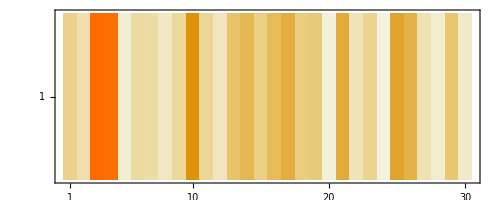

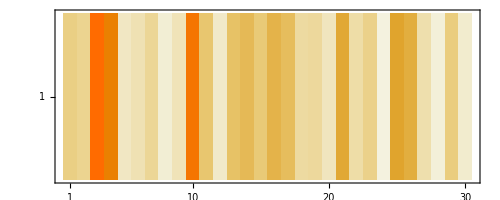

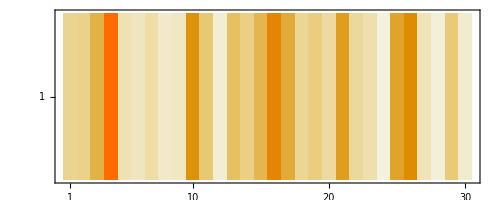

```mathematica
input=RandomReal[1,{7,128}];
statefulnet=NetStateObject[trainedDecoder];
statefulnet[<|"Input" -> input,"predict(t-1)"->{StartOfString}|>, None]//MatrixPlot
statefulnet[<|"Input" -> input,"predict(t-1)"->{StartOfString}|>, None]//MatrixPlot
statefulnet[<|"Input" -> input,"predict(t-1)"->{StartOfString}|>, None]//MatrixPlot
```

```mathematica
statefulnet=NetStateObject[trainedDecoder];
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{StartOfString}|>]
```

{m}

```mathematica
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{"m"}|>]
```

{i}

```mathematica
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{"i"}|>]
```

{s}

```mathematica
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{"s"}|>]
```

{t}

```mathematica
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{"r"}|>]
```

{r}

```mathematica
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{"a"}|>]
```

{l}

```mathematica
statefulnet[<|"Input" -> trainedEncoder[-Graphics-],"predict(t-1)"->{"l"}|>]
```

{EndOfString}

Write a function to apply seq-2-seq decoding to an image:

```mathematica
seq2seqDecode[input_Image] := Module[{encoded,obj},
	encoded = trainedEncoder[input];
	obj = NetStateObject[trainedDecoder];
	StringJoin[
		NestWhileList[
			obj[<|"Input" -> encoded, "predict(t-1)" -> #|>]&, (* apply the net (on step of the recurrence / one character inferred) *)
			{StartOfString}, (* start *)
			!MemberQ[#,EndOfString]&, 1, (* until EndOfString is generated *)
			100
		] /. {StartOfString -> "", EndOfString -> ""}
	]
]
```

```mathematica
AssociationMap[seq2seqDecode,First/@RandomSample[testset,10]]
```

<|-Graphics-→geophysics,-Graphics-→open,-Graphics-→notwithstanding,-Graphics-→pricey,-Graphics-→saddler,-Graphics-→evaporation,-Graphics-→disembowelment,-Graphics-→dieter,-Graphics-→spheroidal,-Graphics-→resurrection|>

Let’s see how does the network:

```mathematica
With[{smallset=RandomSample[testset,100]},
N@Mean@MapThread[EditDistance[#1,#2]&,
{ParallelMap[seq2seqDecode,First/@smallset],
Last/@smallset}]]
```

0.01

```mathematica
seq2seqDecode[-Graphics-]
```

kadiddlehopper

```mathematica
seq2seqDecode[-Graphics-]
```

longseduenceofaracters

```mathematica
seq2seqDecode[-Graphics-]
```

veryharangrarangeotedsyeofeofeofedsharacters

```mathematica
seq2seqDecode[-Graphics-]
```

rxwifyr

```mathematica
seq2seqDecode[-Graphics-]
```

abcdiikhilikliklikthotfomky

```mathematica
seq2seqDecode[-Graphics-]
```

tlizdabbytufiy

## More: Natural Language Processing Applications for Text

Natural Language Processing is a very active and exciting field! Read more:

Question Answering

Tutorial with the bAbI QA  Dataset

Blog post about FindTextualAnswer (using pointer networks)

Language Modeling

Tutorial on Language Modeling

page of Wolfram English Character Level Language Model

Application sections in pages of some Nets:

page of ELMo

page of GPT

page of BERT

## Questions?

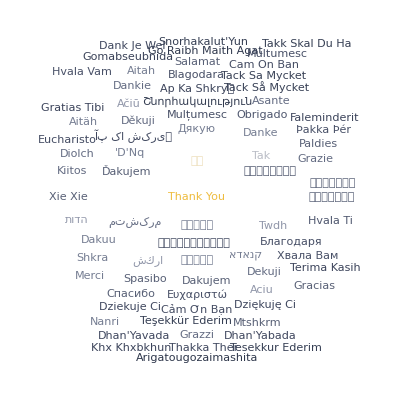

```mathematica
SetOptions[EvaluationNotebook[], WindowTitle -> "Building Applications with Neural Networks"]

ThankYouAll = Last /@ KeySort @ WordTranslation["thank you", All];
ThankYouAll = Values[ThankYouAll];
ThankYouAll = Capitalize[Union[ThankYouAll, Transliterate @ ThankYouAll], "AllWords"];

WordCloud[
	Append[AssociationThread[ThankYouAll -> Map[StringLength[#]^-0.8&, ThankYouAll]],"Thank You"->0.7],
	WordSpacings -> {6,2}, ColorFunction -> ColorData["GrayYellowTones"]
]
```